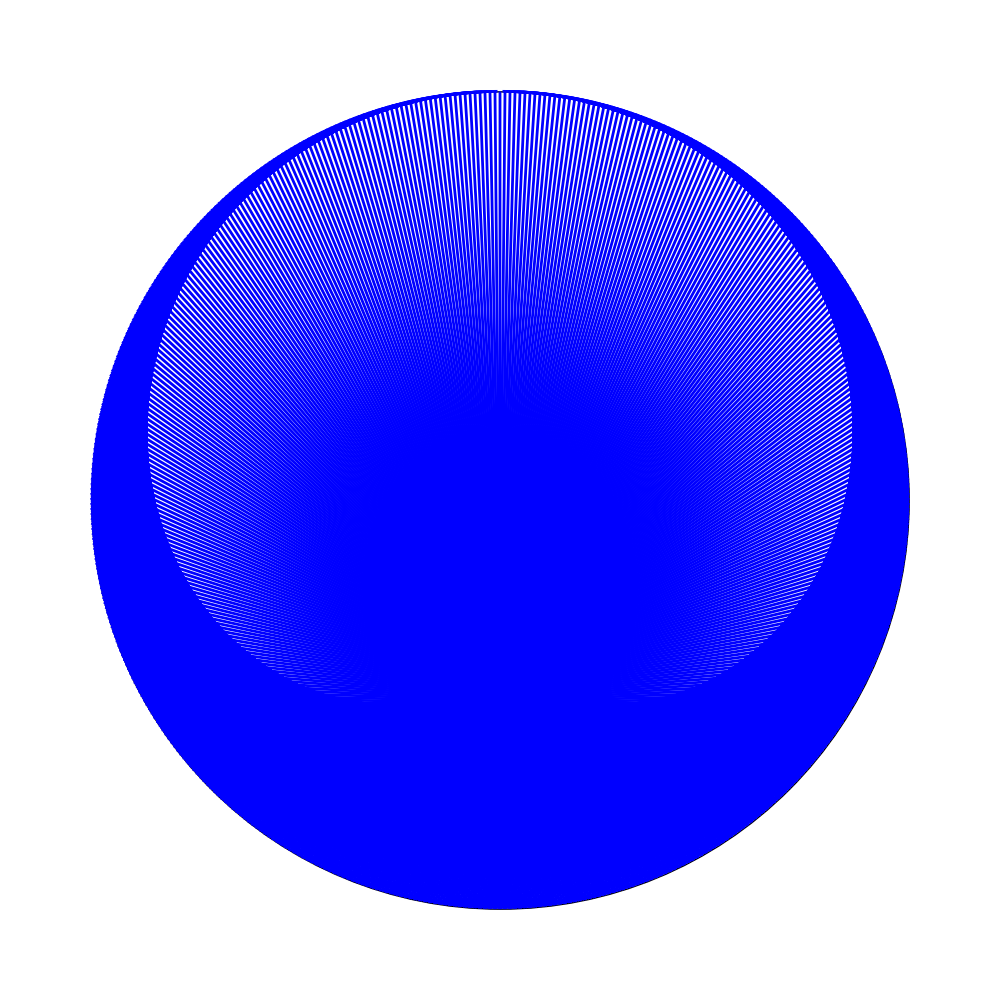

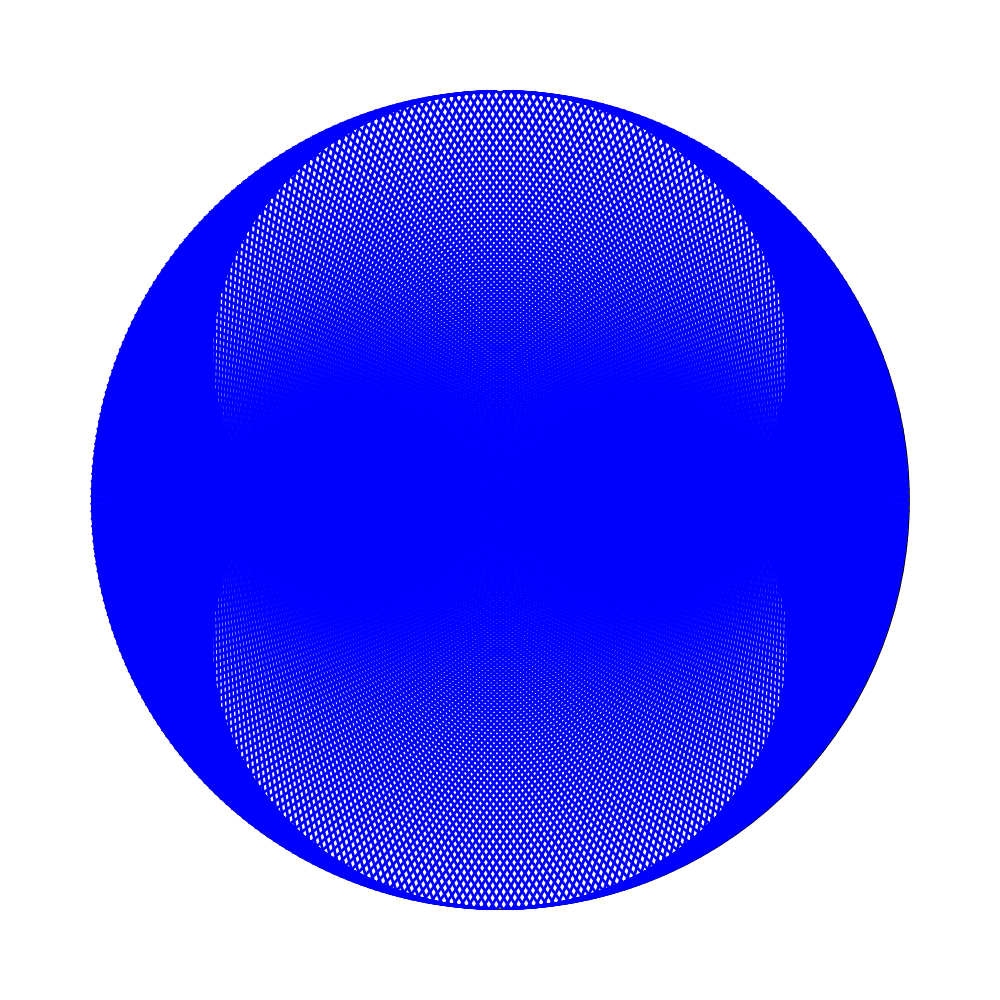

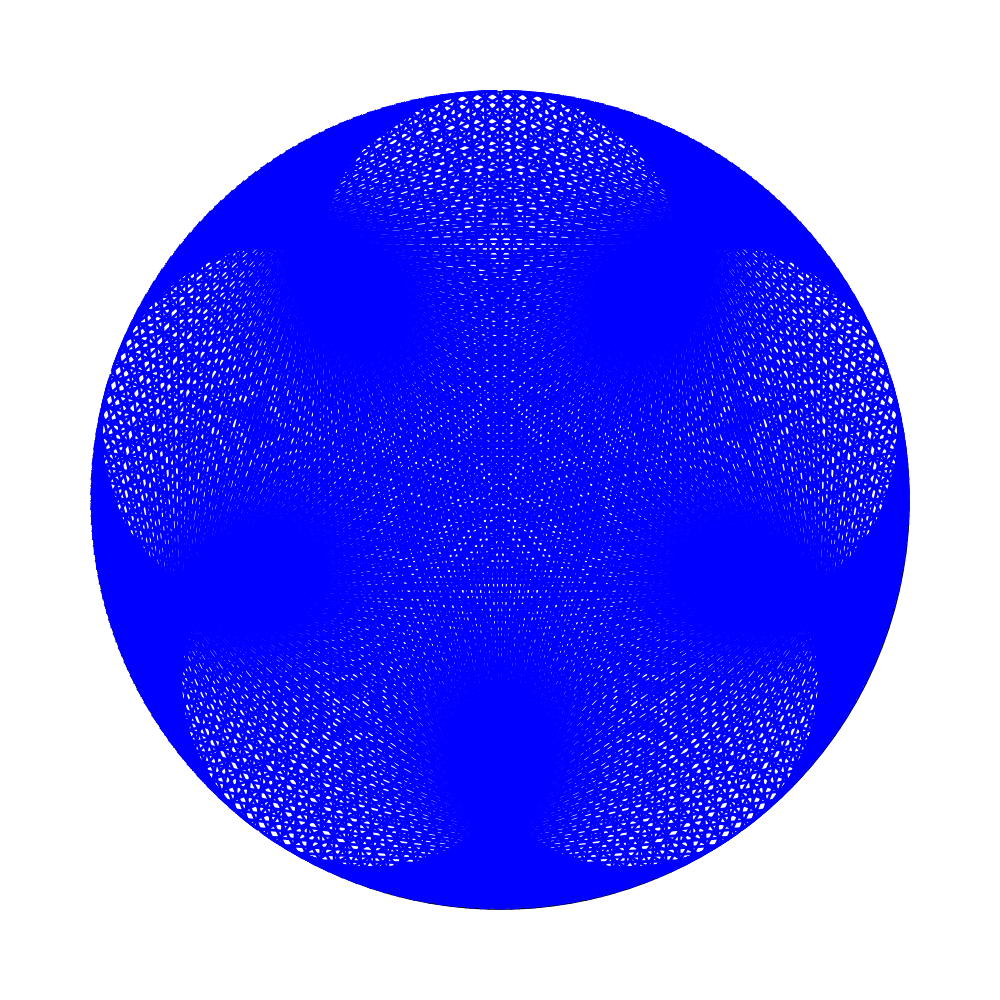

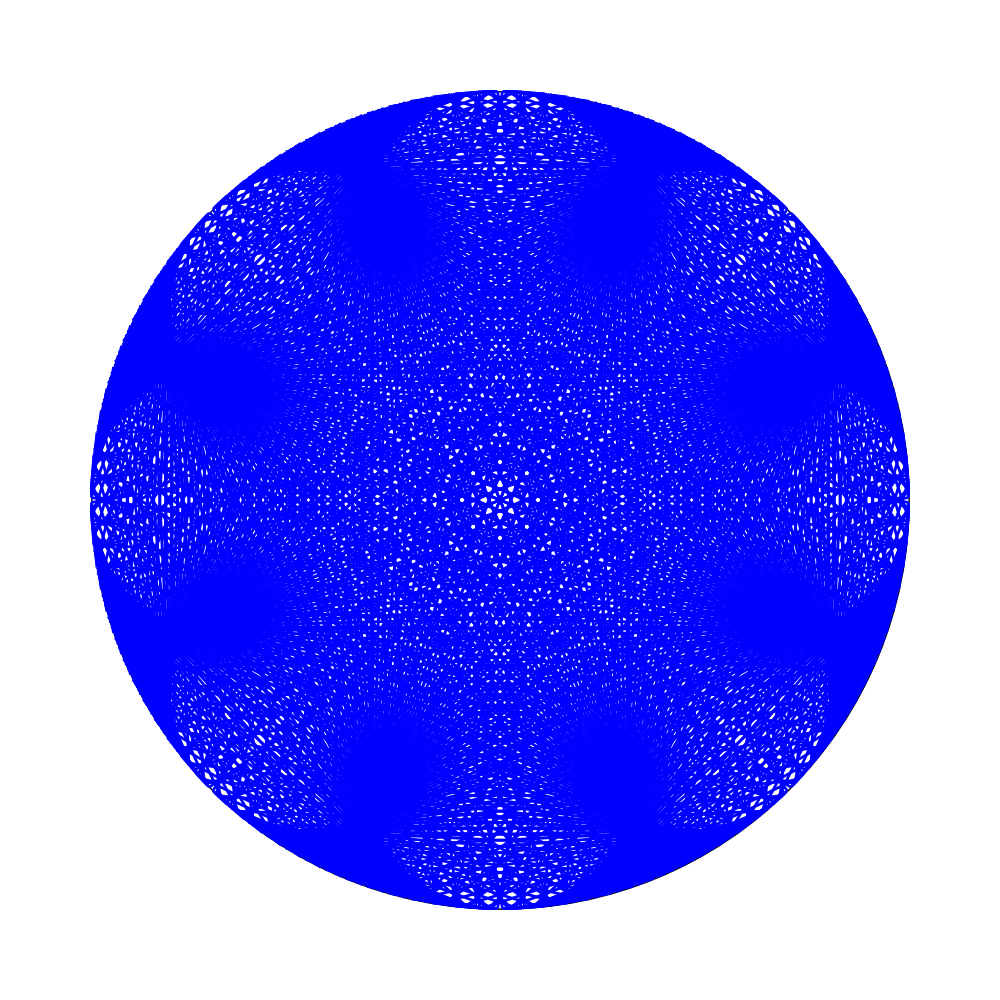

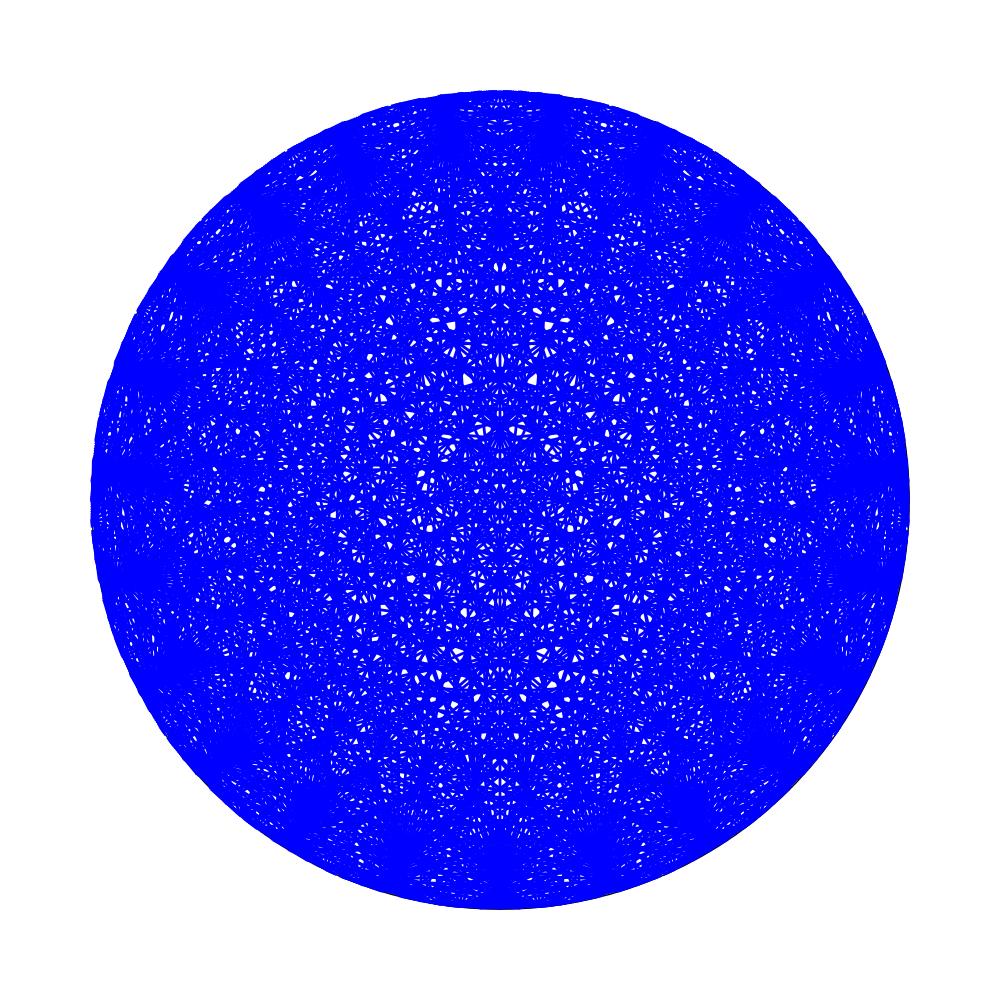

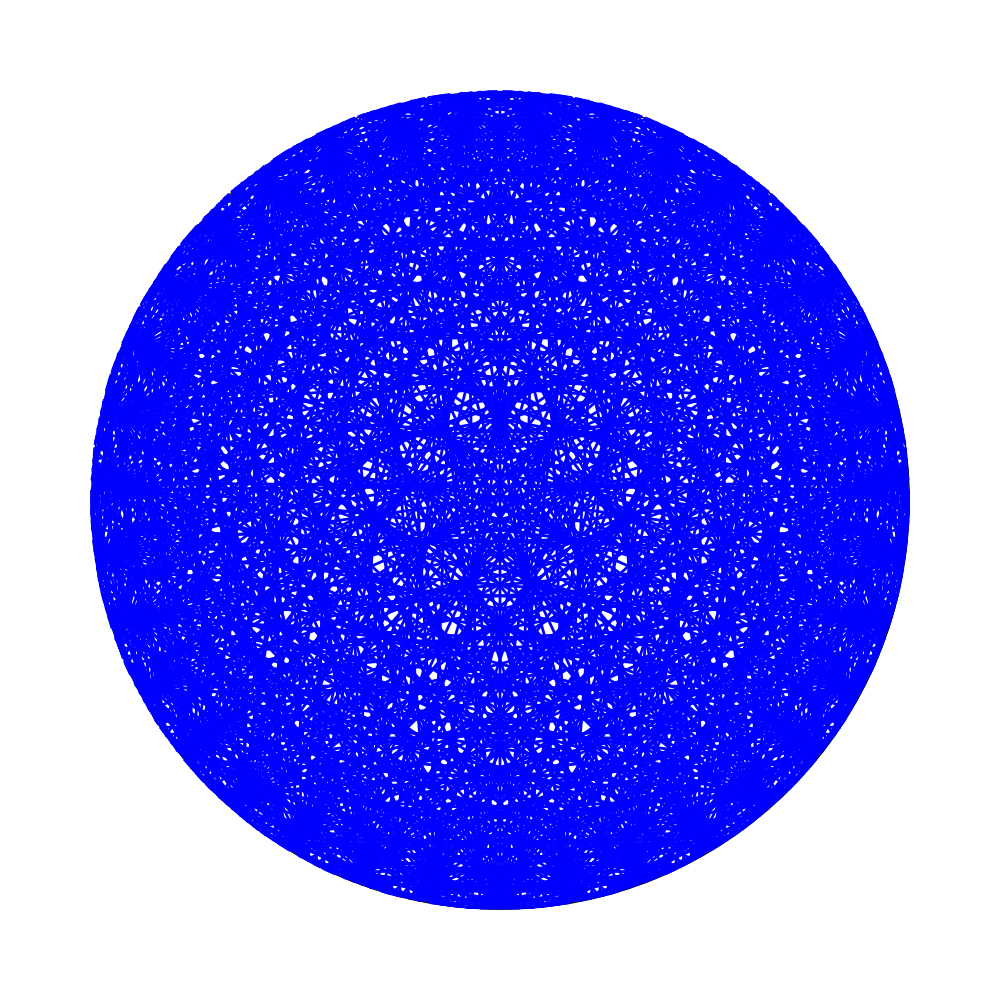

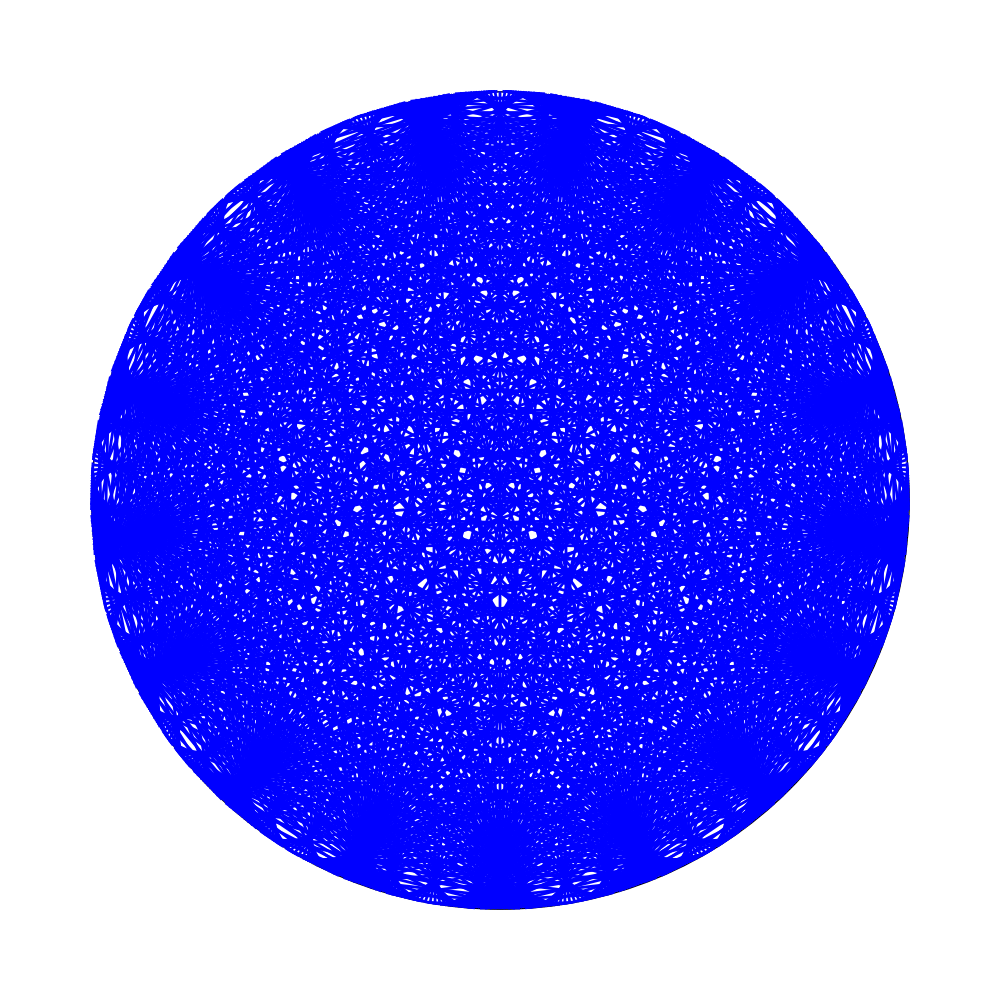

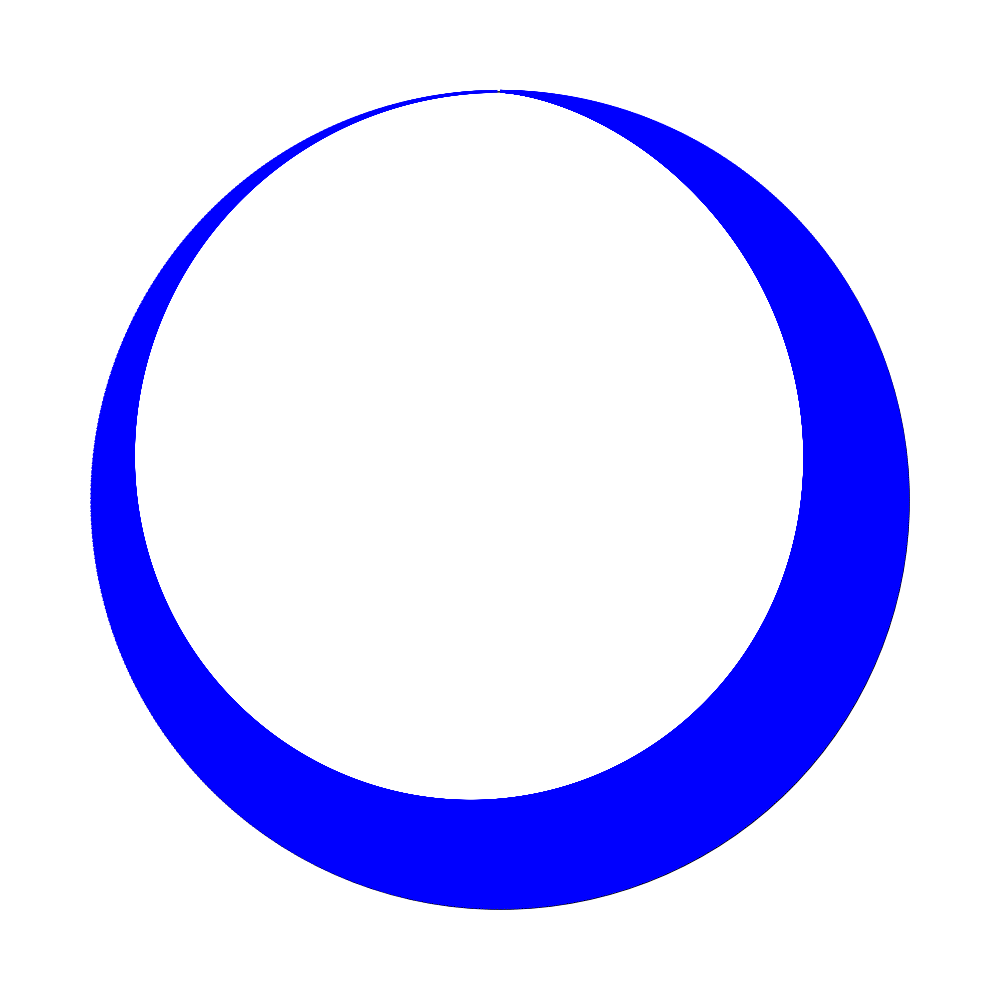

```mathematica
r[t_,radius_]:=(
x=-(radius*Sin[-t]);
y=radius*Cos[-t];
{x,y}
);

r[t_]:=(
r[t,1]
);

line[from_,to_]:=(
Style[Line[{r[2Pi from],r[2Pi to]},VertexColors->{Yellow,Red}],Blue, Thickness[0.002]]
);

afterComma[num_]:=(
num-Floor[num]
);

plot[fun_]:=(
Graphics[{Style[Circle[{0,0},1],Thickness[0.001]],Table[line[n, fun[n]],{n,0,1,1/2^10}]},ImageSize->1000]
);

plot[Function[n, afterComma[n*2]]]
plot[Function[n, afterComma[n*3]]]
plot[Function[n, afterComma[n*6]]]
plot[Function[n, afterComma[n*9]]]
plot[Function[n, afterComma[n*24]]]
plot[Function[n, afterComma[n*36]]]
plot[Function[n, afterComma[n*18]]]
plot[Function[n, afterComma[n^2]]]
plot[Function[n, afterComma[n^3]]]
plot[Function[n, afterComma[n^(1/2)]]]
plot[Function[n, afterComma[n^(1/3)]]]
```